## Pendulum swing up, as a boundary-value problem.

based on Mathematica example for FindRoot (thanks for help from Paul Tupper, SFU Mathematics)
• revised, Nov. 12, 2021:
  – eliminate unused variables from modules
  – add option in NDSolveValue to prevent (spurious) warning messages about InterpolatingFunction
  – simplify Plot and assignment commands

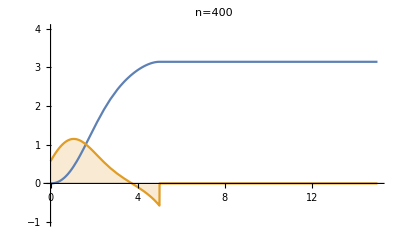

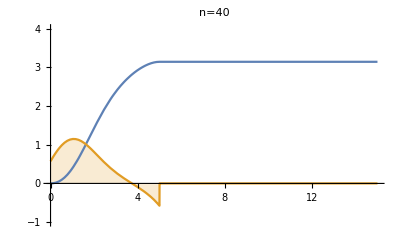

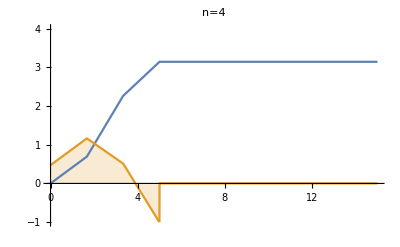

```mathematica
Clear["Global`*"];

ffCalc[n_,τ_,τ1_]:=Module[{f,θ,θdot,λ,λdot,Δt,bcs,eqns,sv,froot,θff0,θdotff0,uff0,θff,θdotff,uff},
Δt=τ/n; 
f[{θ_,θdot_,λ_,λdot_}] := {θdot,-Sin[θ]-λ,λdot,-Cos[θ]λ};
bcs={Subscript[θ, 0]==Subscript[θdot, 0]==Subscript[θdot, n]==0,Subscript[θ, n]==π}; (* hard final constraint *)
eqns=Flatten[Join[bcs, Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}== {Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]} +Δt/2(f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])],{i,1,n}]]]; (* The second part is the euler updates and the first part are the boundary conditions. Together they form the complete set of linear coupled equations *)
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];
uff0=ListInterpolation[Table[-Subscript[λ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];

θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{θff,θdotff,uff}]
τ=5;τ1=3τ;
n=399;{θ1a,θdot1a,u1a}=ffCalc[n,τ,τ1];
p1a=Plot[{θ1a[t],u1a[t]},{t,0,τ1},GridLines->{None,{π}},Filling->{2->Axis},PlotRange->{-1,4},PlotLabel->HoldForm[n=400]]

n=39;{θ2a,θdot2a,u2a}=ffCalc[n,τ,τ1];
p2a=Plot[{θ2a[t],u2a[t]},{t,0,τ1},GridLines->{None,{π}},Filling->{2->Axis},PlotRange->{-1,4},PlotLabel->HoldForm[n=40]]

n=3;{θ3a,θdot3a,u3a}=ffCalc[n,τ,τ1];
p3a=Plot[{θ3a[t],u3a[t]},{t,0,τ1},GridLines->{None,{π}},Filling->{2->Axis},PlotRange->{-1,4},PlotLabel->HoldForm[n=4]]
```

Test the approximate solution on the open-loop
 dynamics (integrated at a fine time step)

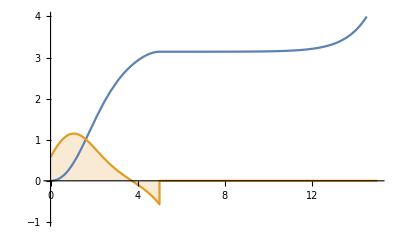

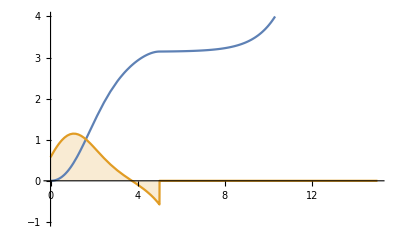

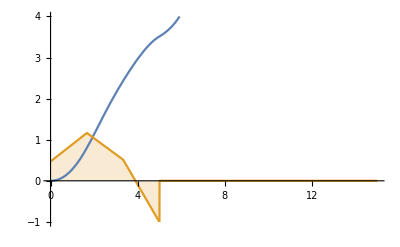

```mathematica
TestSwingUp[τ_,τ1_,uff0_]:=Module[{eq,init,θ,θdot,θs,θdots,uff,t},
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+uff[t]};
init={θ[0]==θdot[0]==0};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
{θs,uff}]

{θ1b,u1b}=TestSwingUp[τ,τ1,u1a];
p1b=Plot[{θ1b[t],u1b[t]},{t,0,τ1},GridLines->{None,{π}},PlotRange->{-1,4},Filling->{2->Axis}]

{θ2b,u2b}=TestSwingUp[τ,τ1,u2a];
p2b=Plot[{θ2b[t],u2b[t]},{t,0,τ1},GridLines->{None,{π}},PlotRange->{-1,4},Filling->{2->Axis}]

{θ3b,u3b}=TestSwingUp[τ,τ1,u3a];
p3b=Plot[{θ3b[t],u3b[t]},{t,0,τ1},GridLines->{None,{π}},PlotRange->{-1,4},Filling->{2->Axis}]
```

Show that linear feedback can stabilize against “bad” numerics

```mathematica
TestSwingUpFB[τ_,τ1_,θff0_,θdotff0_,uff0_]:=Module[{eq,init,θ,θdot,θff,θdotff,uff,t,κ1,κ2,ufb,u,θs,θdots,us},
κ1=κ2=√2+1;  (* lqr for q=r for balancing pendulum *)
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
ufb[t_]:=κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t]);
u[t_]:=uff[t]+ufb[t];
eq={θ'[t]==θdot[t],θdot'[t]==-Sin[θ[t]]+u[t]};
init={θ[0]==θdot[0]==0};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t]);
{θs,us}]
```

```mathematica
{θ1c,u1c}=TestSwingUpFB[τ,τ1,θ1a,θdot1a,u1a];
p1c=Plot[{θ1c[t],u1c[t]},{t,0,τ1},GridLines->{None,{π}},PlotRange->{-1,4},Filling->{2->Axis}];

{θ2c,u2c}=TestSwingUpFB[τ,τ1,θ2a,θdot2a,u2a];
p2c=Plot[{θ2c[t],u2c[t]},{t,0,τ1},GridLines->{None,{π}},PlotRange->{-1,4},Filling->{2->Axis}];

{θ3c,u3c}=TestSwingUpFB[τ,τ1,θ3a,θdot3a,u3a];
p3c=Plot[{θ3c[t],u3c[t]},{t,0,τ1},GridLines->{None,{π}},PlotRange->{-1,4},Filling->{2->Axis}];
```

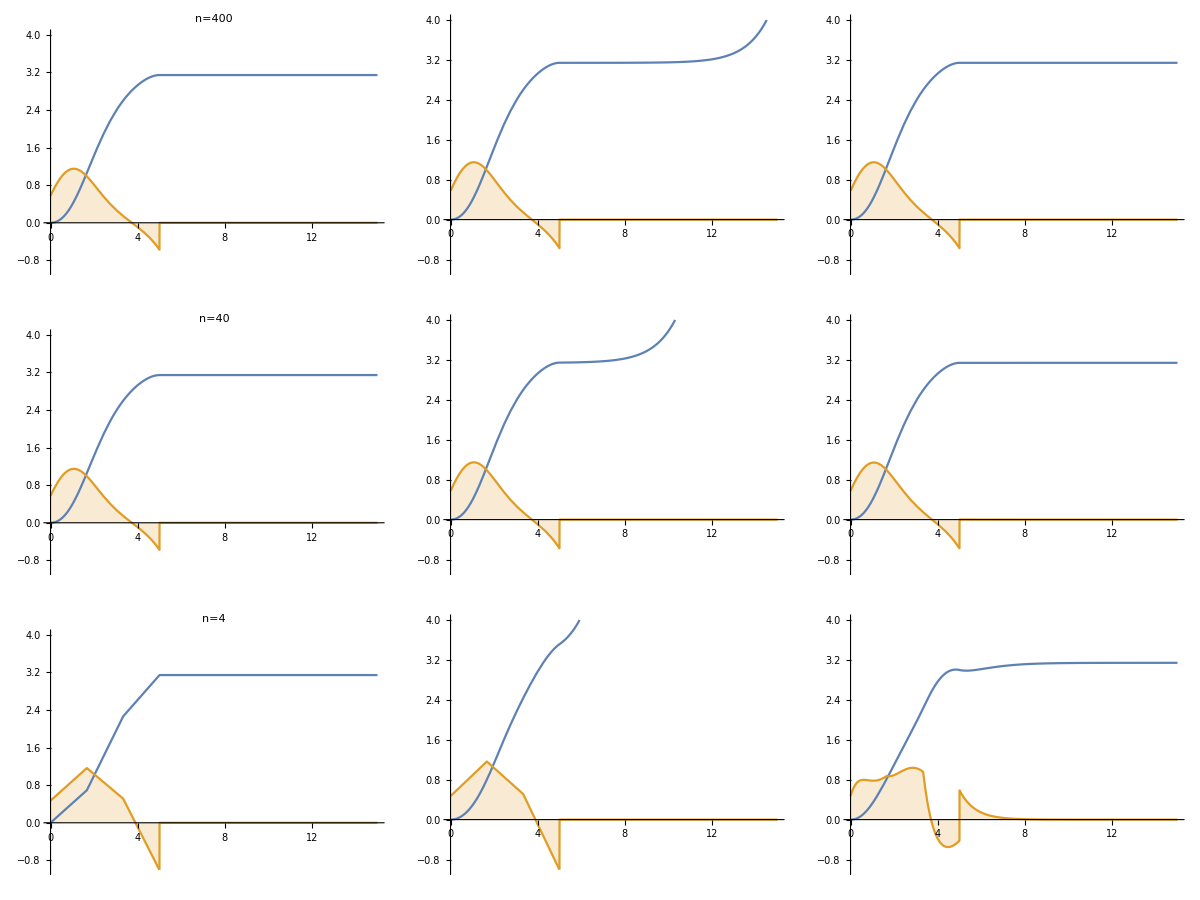

```mathematica
Grid[{{p1a,p1b,p1c},{p2a,p2b,p2c},{p3a,p3b,p3c}},Spacings->{4,3}]
```

Export data

```mathematica
dat=Table[Through[{
θ1a,u1a,θ2a,u2a,θ3a,u3a,
θ1b,u1b,θ2b,u2b,θ3b,u3b,
θ1c,u1c,θ2c,u2c,θ3c,u3c}
[t]],{t,0,τ1,0.05}]//N;
dat1=Table[Through[{
θ3a,u3a,
θ3b,u3b,
θ3c,u3c}
[t]],{t,0,τ1,τ/3}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["swingUpBV.dat", dat];
Export["swingUpBV1.dat", dat1] 
*)
```